```mathematica
Quit[]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/armin/my_programs/alphaLoopMisc/graph_generation/example_ggHH_2Loop

```mathematica
<<"../orientedGraphTools.m"
```

The documented functions in this package are: 
 ?plotGraph 
 ?findIsomorphicGraphs 
 ?constructCuts
 ----------------------------------------- 
 Needs the package IGraphM which can be downloaded from https://github.com/szhorvat/IGraphM. !!! 
 Run: Get["https://raw.githubusercontent.com/szhorvat/IGraphM/master/IGInstaller.m"] for installation

```mathematica
(* Load ggHH 2 Loop graphs *)
```

```mathematica
allGraphs=ToExpression["{"<>StringDrop[StringReplace[Import["ggHH.qgr","Text"],{"**NewDiagram**"->",","\n"->""}]<>"}",1]];
```

```mathematica
exampleGraphs=allGraphs[[2;;3]];
```

```mathematica
(* Lets plot some isomorphic graphs *)
```

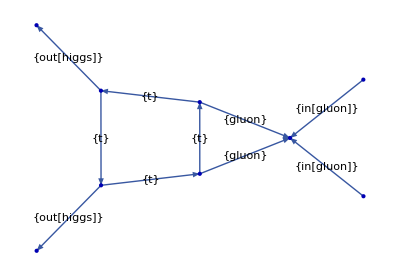

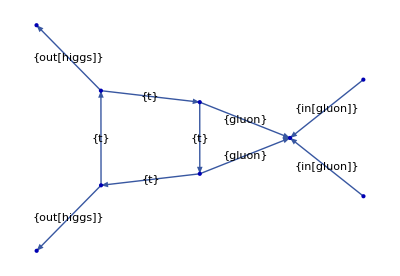

```mathematica
plotGraph[#,edgeLabels->"particleType",plotSize->Scaled[0.3]]&/@(exampleGraphs);
```

```mathematica
(* find the isomorphism *)
```

```mathematica
iso=findIsomorphicGraphs[exampleGraphs,edgeTagging->"particleType"]
```

{{{2,1},{{<|1→1,2→2,3→3,out[1]→out[1],4→4,out[2]→out[2],5→5,in[1]→in[1],in[2]→in[2]|>,Cycles[{}],{1,1,1,1,-1,-1,-1,-1,1,1}},{<|1→1,2→2,3→3,out[1]→out[1],4→4,out[2]→out[2],5→5,in[1]→in[2],in[2]→in[1]|>,Cycles[{{1,2}}],{1,1,1,1,-1,-1,-1,-1,1,1}},{<|1→2,2→1,3→4,out[1]→out[2],4→3,out[2]→out[1],5→5,in[1]→in[1],in[2]→in[2]|>,Cycles[{{3,4},{6,7},{9,10}}],{1,1,1,1,1,1,1,1,1,1}},{<|1→2,2→1,3→4,out[1]→out[2],4→3,out[2]→out[1],5→5,in[1]→in[2],in[2]→in[1]|>,Cycles[{{1,2},{3,4},{6,7},{9,10}}],{1,1,1,1,1,1,1,1,1,1}}}}}

```mathematica
(* looks best *)
iso[[1,2,1]]
```

{<|1→1,2→2,3→3,out[1]→out[1],4→4,out[2]→out[2],5→5,in[1]→in[1],in[2]→in[2]|>,Cycles[{}],{1,1,1,1,-1,-1,-1,-1,1,1}}